```mathematica
U = {{9,0},{12,1}}
d={{E^(3t),0},{0,e^(3t)}}
n={{1,t},{0,1}}
U.d.n.Inverse[U]
```

{{9,0},{12,1}}

{{ⅇ^(3 t),0},{0,e^(3 t)}}

{{1,t},{0,1}}

{{ⅇ^(3 t)-12 ⅇ^(3 t) t,9 ⅇ^(3 t) t},{(4 ⅇ^(3 t))/3-4/3 (e^(3 t)+12 ⅇ^(3 t) t),e^(3 t)+12 ⅇ^(3 t) t}}

```mathematica
MatrixForm[{{ⅇ^(3 t)-12 ⅇ^(3 t) t,9 ⅇ^(3 t) t},{(4 ⅇ^(3 t))/3-4/3 (e^(3 t)+12 ⅇ^(3 t) t),e^(3 t)+12 ⅇ^(3 t) t}}]
```

(ⅇ^(3 t)-12 ⅇ^(3 t) t | 9 ⅇ^(3 t) t
(4 ⅇ^(3 t))/3-4/3 (e^(3 t)+12 ⅇ^(3 t) t) | e^(3 t)+12 ⅇ^(3 t) t)

```mathematica
M={{1,-4,-11,11},{3,-15,-42,42},{-2,12,34,-34},{-1,7,20,-20}}
M.M
```

{{1,-4,-11,11},{3,-15,-42,42},{-2,12,34,-34},{-1,7,20,-20}}

{{0,1,3,-3},{0,3,9,-9},{0,-2,-6,6},{0,-1,-3,3}}

```mathematica
M.M.M
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
{u,j}=JordanDecomposition[M]
```

{{{-11/9,-3,11,0},{-11/3,-9,42,0},{34/9,6,-34,0},{23/9,3,-20,1}},{{0,0,0,0},{0,0,1,0},{0,0,0,1},{0,0,0,0}}}

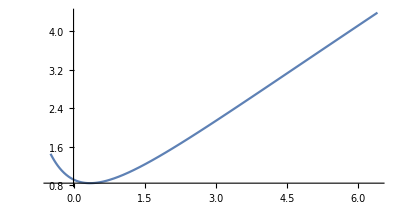

```mathematica
a=0.5;
ParametricPlot[{1+5t+13t^2/2+41t^3/6+121t^4/24+73t^5/24+1093t^6/720,1+2t+7t^2+10t^3/3+61t^4/24+91t^5/60+547t^6/720},{t,-a,a}]
```

```mathematica
s=NDSolve[{y'[x]==y[x]^2+x^2,y[0]==0},y,{x,-2,2}]
```

{{y→InterpolatingFunction[…]}}

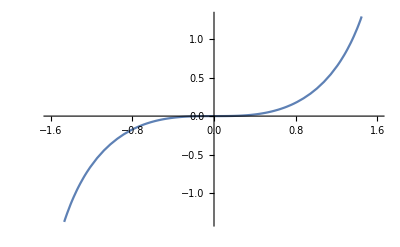

```mathematica
Plot[Evaluate[y[x]/.s],{x,-1.6,1.6}]
```

```mathematica
Integrate[-Sin[s]Log[Cos[s]]-Sin[s]+s Cos[s],{s,0,t}]
```

$Aborted

```mathematica
Integrate[e^(-t r)/Sqrt[r^2+1],{r,0,Infinity}]
```

ConditionalExpression[-BesselJ[0,t Log[e]] Log[1/2 t Log[e]]+1/2 π StruveH[0,t Log[e]]-Hypergeometric0F1Regularized^(1,0)[1,-1/4 t^2 Log[e]^2],Re[t Log[e]]>0]

```mathematica
Integrate[E^(x t)/Sqrt[1+t^2],{t,-Infinity,1}]
```

∫_(-∞)^1 ⅇ^(t x)/(√(1+t^2))ⅆt

```mathematica
Integrate[Sin[x t]/Sqrt[t^2-1],{t,1,Infinity}]
```

Integrate::idiv: Integral of Sin[t x]/(√(-1+t^2)) does not converge on {1,∞}.

∫_1^∞ Sin[t x]/(√(-1+t^2))ⅆt